# atlas.ripe.net - traceroute

How long as TWC been aware of network congestion in High Speed Internet service to Hana, HI?

by Chase.Turner@TFarms.com

## Terminology

### Atlas Raw Data Structures

JSON / JLink -Xmx : http://reference.wolfram.com/mathematica/ref/message/Import/nojmem.html

atlas documentation : https://atlas.ripe.net/docs/data_struct 
RFC4950 ICMP Extensions for Multiprotocol Label Switching : http://tools.ietf.org/html/rfc4950
paris traceroute version : http://www.paris-traceroute.net

howto/AddErrorBarsToChartsAndPlots

## JSON Source

#### fetchJSONMeasurement

```mathematica
ClearAll[importJSON];
Needs["JLink`"];
importJSON[sourceURI_String]:=Module[
{jsonStructure},
(* PREPARE JSON PARSER FOR LARGE FILES  *)
InstallJava[];
(*  HACK trick to ensure large JSON files can be read  *)
ReinstallJava[CommandLine->"java",JVMArguments->"-Xmx2024m"];
(* READ JSON stream *)
jsonStructure=Import[sourceURI,"JSON"];
(* CLEAN UP JSON PARSER *)
UninstallJava[];
(* --->RETURNING *)
jsonStructure
];
```

#### fetchJSONMeasurement

```mathematica
ClearAll[fetchJSONMeasurement];
Needs["JLink`"];
fetchJSONMeasurement[resultNumber_Integer, friendlyName_String]:=Module[
{defaultCacheDir, fullPathToCache,uri, jsonData},

(* Where to find data if on local file system *)
defaultCacheDir=FileNameJoin[{NotebookDirectory[], "data"}];
fullPathToCache=FileNameJoin[{defaultCacheDir,"RIPE-Atlas-measurement - "<>ToString[resultNumber]<>" - "<>friendlyName<>".json"}];

(* Where to find result at atlas.ripe.net *)
uri="https://atlas.ripe.net/api/v1/measurement/"<>ToString[resultNumber]<>"/result";

(* Short-circuit to local file if available *)
If[FileExistsQ[fullPathToCache],
jsonData=importJSON[fullPathToCache],
Module[{},
jsonData=importJSON[uri];
Export[fullPathToCache,jsonData,"JSON"]];
(* --->RETURNING *)
jsonData
]
];
```

#### tData references the JSON data structure for atlas.ripe.net

Select the dataSet and load it in

```mathematica
(* Transpacific Egress *)
egressToMainland={
{1672664,"p17329 - transpacificFrom - 7 probes" },
{1664934,"72.129.45.3 - transpacific - oahu - 7probes"}
};
(* Transpacific Ingresss *)
ingressFromMainland={
{1673867,"p1178 - transpacificFrom - p17329" },
{1672505,"Bill  - transpacificFrom - p17329" },
{1672640,"Marty - transpacificFrom - p17329" }
};
(* Interisland only *)
interislandOnly={
{1672505,"p1178 - interisland - 6 probes" }
};

Clear[tData];
Block[{tMeasurements,dataSets},
dataSets= fetchJSONMeasurement[#[[1]],#[[2]]]&/@ingressFromMainland;
tData=Flatten[dataSets,1];
];
Dimensions[tData]
```

{973}

## Result Patterns

Objective is to correctly identify the patterns of different results.  This section was built iteratively with the nominalPattern, and iterative use of DeleteCases to highlight just those patterns which are not yet understood in the data set.

### Nominal Results to be allowed

```mathematica
nominal={"from"->from_String,"rtt"->rtt_, "size"->size_Integer,"ttl"->ttl_Integer};
nominalIttl={"from"->from_String,"ittl"->ittl_Integer,"rtt"->rtt_, "size"->size_Integer,"ttl"->ttl_Integer};
nominalICMPext={"from"->from_String,"icmpext"->icmpext_List,"rtt"->rtt_, "size"->size_Integer,"ttl"->ttl_Integer};
nominalIttlICMPext={"from"->from_String,"icmpext"->icmpext_List,"ittl"->ittl_Integer,"rtt"->rtt_, "size"->size_Integer,"ttl"->ttl_Integer};

nominals=Alternatives@@{nominal, nominalIttl,nominalICMPext,nominalIttlICMPext };
```

### If any of the following appear in a traceroute, you should ignore the entire traceroute

It may sound draconian, but the happy path analysis is for the general case of success.  If at some later time there is a need to understand and highlight these exceptions, the patterns are here to match.

```mathematica
tossOutAstrix={"x"->"*"};
tossOutLate={___,"late"->_,___};
tossOutEDST={"edst"->edst_,"from"->edstFrom_,___};
tossOutErrorN={"err"->errString_String,"from"->errorFrom_,___};
tossOutDup={"dup"->dup_,___};
(* various error types *)
(* "name resolution failed..." *)
(* "sendto failed: Network is unreachable" *)
tossOutError={"error"->errorString_String};

tossTheseResultsOut=Alternatives@@{tossOutAstrix,tossOutLate,tossOutEDST,tossOutErrorN,tossOutError,tossOutDup};
```

### How many flattened results fall into ether category?

```mathematica
expectedPatterns=Join[nominals,tossTheseResultsOut];
```

#### Slicing function to get all results flattened

```mathematica
tDataResultsAll=Flatten[tData[[All,13,2,All,2,2]],2];
```

#### Iteration on results until there are no more...

To answer this question, the results need to be flattened.  This is the combination of Flatten and slices to reach the results of all hops

```mathematica
tDataResultsAll[[1;;2]]//TableForm
```

Integer[] |  |  | 
from→192.168.1.1 | rtt→2.516 | size→68 | ttl→64

Keep in mind that I defined “nominals” and “throwOutThese” by iterating with DeleteCases until an empty set was returned.  Hence, if you are at this point with a data set and there is a non-empty data set appearing in the code below, you have discovered a new pattern that is to either be processed as accepted, or thrown out!

```mathematica
DeleteDuplicates[DeleteCases[tDataResultsAll,expectedPatterns]]
```

{Integer[]}

#### Summarize Matches

```mathematica
Block[{tDataLength, tDataNominal,tDataToToss},
{tDataLength, tDataNominal,tDataToToss}=Length/@{
tDataResultsAll,
Cases[tDataResultsAll,nominals], Cases[tDataResultsAll,tossTheseResultsOut]
};

{{"TotalCount", "nominal", "toToss", "Toss %age"},
{tDataLength, tDataNominal,tDataToToss,100N[tDataToToss/tDataLength]}}]//TableForm
```

TotalCount | nominal | toToss | Toss %age
132295 | 126794 | 5499 | 4.15662

## 100% Nominal Results Only

```mathematica
keepThisTracerouteTestP[aTracerouteResult_]:=Block[{hopResults,matched},
hopResults="result"/.aTracerouteResult;

(* Answer with False if there are no results, or there is an error in the main result list; otherwise, evaluate evaluate remaining. *)
If[And[
Length[hopResults]>0,
0==Length[Cases[hopResults,tossOutError]]],
0==Length[Cases[Flatten[hopResults[[All,2,2]],1],tossTheseResultsOut]],
(* error such as "name resolution failed" here *)False]
];
```

tDataNominal will be the tData results to evaluate

```mathematica
tDataNominal=Select[tData,keepThisTracerouteTestP];

Block[{tDataL, tDataNominalL},
{tDataL,tDataNominalL} = {Length[tData],Length[tDataNominal]};
{{"allResults","nominal", "%"},{tDataL,tDataNominalL,N[tDataNominalL/tDataL]100}}]//TableForm
```

allResults | nominal | %
973 | 522 | 53.6485

## Semi Nominal Results

When the traceroute faces considerable network congestion, the following algorithm salvages as many of the individual segment tests as is possible.  Measurements from this set should take into account there is a potential loss of information due to failed RTT interval tests removed from the data set.

Frame the above relative to what % of measurments are available, versus the 100% Nominal Results only

```mathematica
scrubIntervalsOfTraceroute[aTracerouteResult_]:=Block[{resultsNotScrubbed,resultsScrubbed,modifiedTraceroute,scrubbingAllowed},

resultsNotScrubbed="result"/.aTracerouteResult;
modifiedTraceroute=aTracerouteResult;

(* Scrub only when there are results which are not holding an error. *)
scrubbingAllowed=And[ArrayDepth[resultsNotScrubbed]==2,0==Length[Cases[resultsNotScrubbed,tossOutError]]];

If[scrubbingAllowed,
resultsScrubbed={#[[1]],"result"->Cases[#[[2,2]],nominals]}&/@resultsNotScrubbed,
(* do nothing *)resultsScrubbed= resultsNotScrubbed];

(* ---> RETURNING *)
modifiedTraceroute
];
```

Revise tData so that the maximal set of nomal results are available

```mathematica
tDataScrubbed=Select[scrubIntervalsOfTraceroute/@tData,keepThisTracerouteTestP];
Length[tDataScrubbed]
```

522

## Pure Nominal Results Only

```mathematica
keepThisTracerouteTestP[aTracerouteResult_]:=Block[{hopResults,matched},
hopResults="result"/.aTracerouteResult;

(* If the result set is not an immediate error, evaluate remaining. *)
If[0==Length[Cases[hopResults,tossOutError]],
0==Length[Cases[Flatten[hopResults[[All,2,2]],1],tossTheseResultsOut]],
(* error such as "name resolution failed" here *)False]
];
```

tDataNominal will be the tData results to evaluate

```mathematica
tDataNominal=Select[tData,keepThisTracerouteTestP];

Block[{tDataL, tDataNominalL},
{tDataL,tDataNominalL} = {Length[tData],Length[tDataNominal]};
{{"allResults","nominal", "%"},{tDataL,tDataNominalL,N[tDataNominalL/tDataL]100}}]//TableForm
```

allResults | nominal | %
973 | 522 | 53.6485

tDataScrubbed will include partial results that were considered to be “normal”

```mathematica
Block[{tDataL, tDataNominalL},
{tDataL,tDataNominalL} = {Length[tData],Length[tDataScrubbed]};
{{"allResults","nominal", "%"},{tDataL,tDataNominalL,N[tDataNominalL/tDataL]100}}]//TableForm
```

allResults | nominal | %
973 | 522 | 53.6485

## Nominal Paths as DiscreteData

```mathematica
ClearAll[ifUnroutableUseFromIP];
ifUnroutableUseFromIP::usage="Ensure common non routable IPv4 addresses are suffixed with their probe name";
(* MESSAGES *)
ifUnroutableUseFromIP::unexpectedArg="probeID->`1`, IPv4->`2`";
(* IMPLEMENTATION *)
ifUnroutableUseFromIP[fromIP_String,ipV4_String/; StringMatchQ[ipV4,"192.168."~~___]]:=fromIP;
ifUnroutableUseFromIP[fromIP_String ,ipV4_String/; StringMatchQ[ipV4,"10."~~___]]:=fromIP;
ifUnroutableUseFromIP[fromIP_String,ipV4_String/; StringMatchQ[ipV4,"172."~~Alternatives @@ToString /@Range[16,31]~~"."~~___]]:=fromIP;
(* The following is the general case where anything else should be the IPv4 address *)
ifUnroutableUseFromIP[fromIP_String ,ipV4_String]:=ifUnroutableUseFromIP[fromIP,ipV4]=ipV4;

(* SPECIAL CASE for ASTRIX routed values *)
ifUnroutableUseFromIP[fromIP_String,prbID_Integer]:=prbID;
```

Define criterian to throw out a traceroute

```mathematica
ClearAll[routeAsDiscreteData];

routeAsDiscreteData[aTraceroute_]:=Block[{
filteredTraceroute,hopResults, prbId,fromIP, hopsAsOrderedList},

{prbId,fromIP}={"prb_id","from"}/. aTraceroute;
filteredTraceroute=aTraceroute;
hopResults =filteredTraceroute[[13,2]];

hopsAsOrderedList=Flatten[DeleteDuplicates[Cases[#[[2,2,All]],nominals:>from]],1]&/@ hopResults;

ifUnroutableUseFromIP[fromIP,#]&/@Flatten[{prbId,hopsAsOrderedList[[1;;]]}]

];
```

#### tDataNominalPaths

```mathematica
tDataNominalPaths=Rule@@#&/@Partition[#,2,1]&/@DeleteDuplicates[routeAsDiscreteData/@tDataNominal];
tDataScrubbedPaths =Rule@@#&/@Partition[#,2,1]&/@DeleteDuplicates[routeAsDiscreteData/@tDataScrubbed];
```

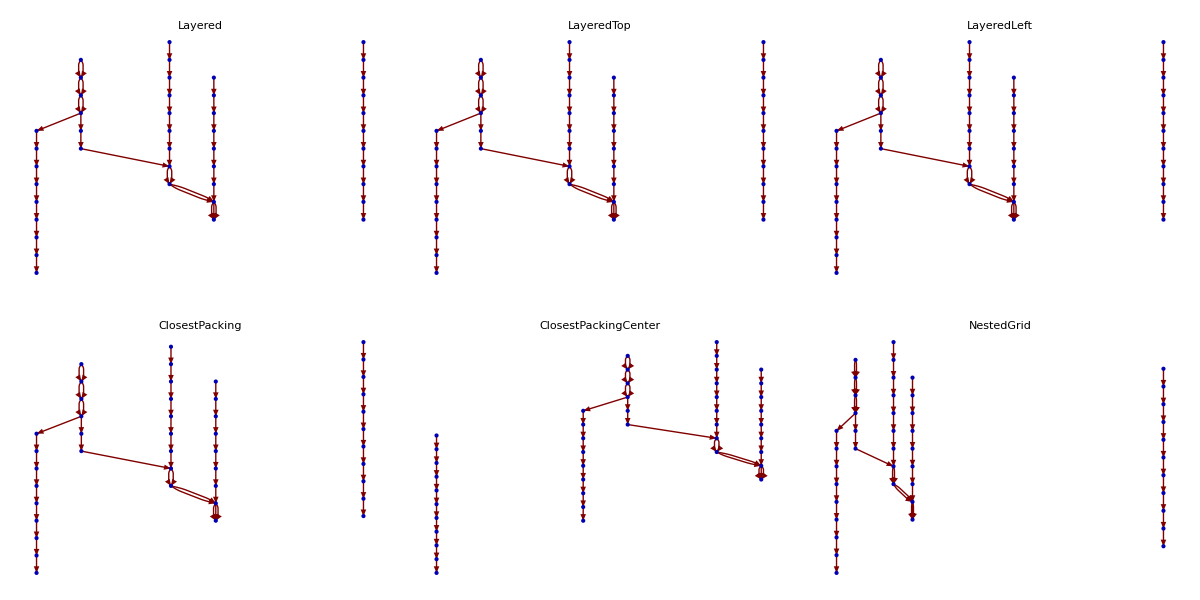

```mathematica
Grid@Partition[Table[LayeredGraphPlot[Flatten[tDataScrubbedPaths,1],
PackingMethod->m,
 DirectedEdges->True,
PlotLabel->Style[m,Small],BaselinePosition->Top,
VertexLabeling->Automatic,
MultiedgeStyle->True,
SelfLoopStyle->None],{m,{"Layered","LayeredTop","LayeredLeft","ClosestPacking","ClosestPackingCenter","NestedGrid"}}],3]
```

## WolframCommentary

My understanding is that you want to rearrange the data so that it doesn’t look like a bunch of messy rules, but so that it looks something like this:

{“prb_id”, “proto”, “paris_id”, “msm_id”, “timestamp”, “type”, “endtime”,
	{ (* now unwind nested hops here ordered by hop number, 
		except my goal here is to transcode the three 
		nested tests for each hop into a summary statstic *)
		{“hop”, “from”, “flags”, “icmpext”, Min[“rtt”], Average[“rtt”], Max[“rtt”] }
	(* but how to handle cases where there is an optional “error” *)
		{“error”, “from”, “flags”, “icmpext”, {}}
	}


Most entries are pretty simple - the only tricky part is dealing with the hop data (the 13th subelement) since that is a deeply nested subelement.

For example, if you wanted to assemble a list of {“prb_id”,”proto”,”paris_id”}, you could do the following:

```mathematica
Transpose@{tData[[All,11,2]],tData[[All,12,2]],tData[[All,10,2]]}
```

{{TCP,{{error→name resolution failed: nodename nor servname provided, or not known}},17329},{1165,ICMP,1},{14720,ICMP,1},{12735,ICMP,1},{10546,ICMP,1},{15111,ICMP,1},{2289,ICMP,1},{1165,ICMP,2},{14720,ICMP,2},{12735,ICMP,2},{10546,ICMP,2},{15111,ICMP,2},{2289,ICMP,2},{1165,ICMP,3},{14720,ICMP,3},{12735,ICMP,3},{10546,ICMP,3},{15111,ICMP,3},{2289,ICMP,3},{1165,ICMP,4},{14720,ICMP,4},{12735,ICMP,4},{10546,ICMP,4},{15111,ICMP,4},{2289,ICMP,4},{1165,ICMP,5},{14720,ICMP,5},{12735,ICMP,5},{10546,ICMP,5},{15111,ICMP,5},{2289,ICMP,5},{1165,ICMP,6},{14720,ICMP,6},{12735,ICMP,6},{10546,ICMP,6},{15111,ICMP,6},{2289,ICMP,6},{1165,ICMP,7},{14720,ICMP,7},{12735,ICMP,7},{10546,ICMP,7},{15111,ICMP,7},{2289,ICMP,7},{1165,ICMP,8},{14720,ICMP,8},{12735,ICMP,8},{10546,ICMP,8},{15111,ICMP,8},{2289,ICMP,8},{1165,ICMP,9},{14720,ICMP,9},{12735,ICMP,9},{10546,ICMP,9},{15111,ICMP,9},{2289,ICMP,9},{1165,ICMP,10},{14720,ICMP,10},{12735,ICMP,10},{10546,ICMP,10},{15111,ICMP,10},{2289,ICMP,10},{1165,ICMP,11},{14720,ICMP,11},{12735,ICMP,11},{10546,ICMP,11},{15111,ICMP,11},{2289,ICMP,11},{1165,ICMP,12},{14720,ICMP,12},{12735,ICMP,12},{10546,ICMP,12},{15111,ICMP,12},{2289,ICMP,12},{1165,ICMP,13},{14720,ICMP,13},{12735,ICMP,13},{10546,ICMP,13},{15111,ICMP,13},{2289,ICMP,13},{1165,ICMP,14},{14720,ICMP,14},{12735,ICMP,14},{10546,ICMP,14},{15111,ICMP,14},{2289,ICMP,14},{1165,ICMP,15},{14720,ICMP,15},{12735,ICMP,15},{10546,ICMP,15},{15111,ICMP,15},{2289,ICMP,15},{1165,ICMP,0},{14720,ICMP,0},{12735,ICMP,0},{10546,ICMP,0},{15111,ICMP,0},{2289,ICMP,0},{1165,ICMP,1},{14720,ICMP,1},{12735,ICMP,1},{10546,ICMP,1},{15111,ICMP,1},{2289,ICMP,1},{1165,ICMP,2},{14720,ICMP,2},{12735,ICMP,2},{10546,ICMP,2},{15111,ICMP,2},{2289,ICMP,2},{1165,ICMP,3},{14720,ICMP,3},{12735,ICMP,3},{10546,ICMP,3},{15111,ICMP,3},{2289,ICMP,3},{1165,ICMP,4},{14720,ICMP,4},{12735,ICMP,4},{10546,ICMP,4},{15111,ICMP,4},{2289,ICMP,4},{1165,ICMP,5},{14720,ICMP,5},{12735,ICMP,5},{10546,ICMP,5},{15111,ICMP,5},{2289,ICMP,5},{1165,ICMP,6},{14720,ICMP,6},{12735,ICMP,6},{10546,ICMP,6},{15111,ICMP,6},{2289,ICMP,6},{1165,ICMP,7},{14720,ICMP,7},{12735,ICMP,7},{10546,ICMP,7},{15111,ICMP,7},{2289,ICMP,7},{1165,ICMP,8},{14720,ICMP,8},{12735,ICMP,8},{10546,ICMP,8},{15111,ICMP,8},{2289,ICMP,8},{1165,ICMP,9},{14720,ICMP,9},{12735,ICMP,9},{10546,ICMP,9},{15111,ICMP,9},{2289,ICMP,9},{1165,ICMP,10},{14720,ICMP,10},{12735,ICMP,10},{10546,ICMP,10},{15111,ICMP,10},{2289,ICMP,10},{1165,ICMP,11},{14720,ICMP,11},{12735,ICMP,11},{10546,ICMP,11},{15111,ICMP,11},{2289,ICMP,11},{1165,ICMP,12},{14720,ICMP,12},{12735,ICMP,12},{10546,ICMP,12},{15111,ICMP,12},{2289,ICMP,12},{1165,ICMP,13},{14720,ICMP,13},{12735,ICMP,13},{10546,ICMP,13},{15111,ICMP,13},{2289,ICMP,13},{1165,ICMP,14},{14720,ICMP,14},{12735,ICMP,14},{10546,ICMP,14},{15111,ICMP,14},{2289,ICMP,14},{1165,ICMP,15},{14720,ICMP,15},{12735,ICMP,15},{10546,ICMP,15},{15111,ICMP,15},{2289,ICMP,15},{1165,ICMP,0},{14720,ICMP,0},{12735,ICMP,0},{10546,ICMP,0},{15111,ICMP,0},{2289,ICMP,0},{1165,ICMP,1},{14720,ICMP,1},{12735,ICMP,1},{10546,ICMP,1},{15111,ICMP,1},{2289,ICMP,1},{1165,ICMP,2},{14720,ICMP,2},{12735,ICMP,2},{10546,ICMP,2},{15111,ICMP,2},{2289,ICMP,2},{1165,ICMP,3},{14720,ICMP,3},{12735,ICMP,3},{10546,ICMP,3},{15111,ICMP,3},{2289,ICMP,3},{1165,ICMP,4},{14720,ICMP,4},{12735,ICMP,4},{10546,ICMP,4},{15111,ICMP,4},{2289,ICMP,4},{1165,ICMP,5},{14720,ICMP,5},{12735,ICMP,5},{10546,ICMP,5},{15111,ICMP,5},{2289,ICMP,5},{1165,ICMP,6},{14720,ICMP,6},{12735,ICMP,6},{10546,ICMP,6},{15111,ICMP,6},{2289,ICMP,6},{1165,ICMP,7},{14720,ICMP,7},{12735,ICMP,7},{10546,ICMP,7},{15111,ICMP,7},{2289,ICMP,7},{1165,ICMP,8},{14720,ICMP,8},{12735,ICMP,8},{10546,ICMP,8},{15111,ICMP,8},{2289,ICMP,8},{1165,ICMP,9},{14720,ICMP,9},{12735,ICMP,9},{10546,ICMP,9},{15111,ICMP,9},{2289,ICMP,9},{1165,ICMP,10},{14720,ICMP,10},{12735,ICMP,10},{10546,ICMP,10},{15111,ICMP,10},{2289,ICMP,10},{1165,ICMP,11},{14720,ICMP,11},{12735,ICMP,11},{10546,ICMP,11},{15111,ICMP,11},{2289,ICMP,11},{ICMP,{{error→name resolution failed: non-recoverable failure in name resolution (1)}},1165},{14720,ICMP,12},{12735,ICMP,12},{10546,ICMP,12},{15111,ICMP,12},{2289,ICMP,12},{1165,ICMP,12},{14720,ICMP,13},{12735,ICMP,13},{10546,ICMP,13},{15111,ICMP,13},{2289,ICMP,13},{1165,ICMP,13},{14720,ICMP,14},{12735,ICMP,14},{10546,ICMP,14},{15111,ICMP,14},{2289,ICMP,14},{1165,ICMP,14},{14720,ICMP,15},{12735,ICMP,15},{10546,ICMP,15},{15111,ICMP,15},{2289,ICMP,15},{1165,ICMP,15},{14720,ICMP,0},{12735,ICMP,0},{10546,ICMP,0},{15111,ICMP,0},{2289,ICMP,0},{1165,ICMP,0},{14720,ICMP,1},{12735,ICMP,1},{10546,ICMP,1},{15111,ICMP,1},{2289,ICMP,1},{1165,ICMP,1},{14720,ICMP,2},{12735,ICMP,2},{10546,ICMP,2},{15111,ICMP,2},{2289,ICMP,2},{1165,ICMP,2},{14720,ICMP,3},{12735,ICMP,3},{10546,ICMP,3},{15111,ICMP,3},{2289,ICMP,3},{1165,ICMP,3},{14720,ICMP,4},{12735,ICMP,4},{10546,ICMP,4},{15111,ICMP,4},{2289,ICMP,4},{1165,ICMP,4},{14720,ICMP,5},{12735,ICMP,5},{10546,ICMP,5},{15111,ICMP,5},{2289,ICMP,5},{1165,ICMP,5},{14720,ICMP,6},{12735,ICMP,6},{10546,ICMP,6},{15111,ICMP,6},{2289,ICMP,6},{1165,ICMP,6},{14720,ICMP,7},{12735,ICMP,7},{10546,ICMP,7},{15111,ICMP,7},{2289,ICMP,7},{1165,ICMP,7},{14720,ICMP,8},{12735,ICMP,8},{10546,ICMP,8},{15111,ICMP,8},{2289,ICMP,8},{1165,ICMP,8},{14720,ICMP,9},{12735,ICMP,9},{10546,ICMP,9},{15111,ICMP,9},{2289,ICMP,9},{1165,ICMP,9},{14720,ICMP,10},{12735,ICMP,10},{10546,ICMP,10},{15111,ICMP,10},{2289,ICMP,10},{1165,ICMP,10},{14720,ICMP,11},{12735,ICMP,11},{10546,ICMP,11},{15111,ICMP,11},{2289,ICMP,11},{1165,ICMP,11},{14720,ICMP,12},{12735,ICMP,12},{10546,ICMP,12},{15111,ICMP,12},{2289,ICMP,12},{1165,ICMP,12},{14720,ICMP,13},{12735,ICMP,13},{10546,ICMP,13},{15111,ICMP,13},{2289,ICMP,13},{1165,ICMP,13},{14720,ICMP,14},{12735,ICMP,14},{10546,ICMP,14},{15111,ICMP,14},{2289,ICMP,14},{1165,ICMP,14},{14720,ICMP,15},{12735,ICMP,15},{10546,ICMP,15},{15111,ICMP,15},{2289,ICMP,15},{1165,ICMP,15},{14720,ICMP,0},{12735,ICMP,0},{10546,ICMP,0},{15111,ICMP,0},{2289,ICMP,0},{1165,ICMP,0},{14720,ICMP,1},{12735,ICMP,1},{10546,ICMP,1},{15111,ICMP,1},{2289,ICMP,1},{1165,ICMP,1},{14720,ICMP,2},{12735,ICMP,2},{10546,ICMP,2},{15111,ICMP,2},{2289,ICMP,2},{1165,ICMP,2},{14720,ICMP,3},{12735,ICMP,3},{10546,ICMP,3},{15111,ICMP,3},{2289,ICMP,3},{1165,ICMP,3},{14720,ICMP,4},{12735,ICMP,4},{10546,ICMP,4},{15111,ICMP,4},{2289,ICMP,4},{1165,ICMP,4},{14720,ICMP,5},{12735,ICMP,5},{10546,ICMP,5},{15111,ICMP,5},{2289,ICMP,5},{1165,ICMP,5},{14720,ICMP,6},{12735,ICMP,6},{10546,ICMP,6},{15111,ICMP,6},{2289,ICMP,6},{1165,ICMP,6},{14720,ICMP,7},{12735,ICMP,7},{10546,ICMP,7},{15111,ICMP,7},{2289,ICMP,7},{1165,ICMP,7},{14720,ICMP,8},{12735,ICMP,8},{10546,ICMP,8},{15111,ICMP,8},{2289,ICMP,8},{1165,ICMP,8},{14720,ICMP,9},{12735,ICMP,9},{10546,ICMP,9},{15111,ICMP,9},{2289,ICMP,9},{1165,ICMP,9},{14720,ICMP,10},{12735,ICMP,10},{10546,ICMP,10},{15111,ICMP,10},{2289,ICMP,10},{1165,ICMP,10},{14720,ICMP,11},{12735,ICMP,11},{10546,ICMP,11},{15111,ICMP,11},{2289,ICMP,11},{1165,ICMP,11},{14720,ICMP,12},{12735,ICMP,12},{10546,ICMP,12},{15111,ICMP,12},{2289,ICMP,12},{1165,ICMP,12},{14720,ICMP,13},{12735,ICMP,13},{10546,ICMP,13},{15111,ICMP,13},{2289,ICMP,13},{1165,ICMP,13},{14720,ICMP,14},{12735,ICMP,14},{10546,ICMP,14},{15111,ICMP,14},{2289,ICMP,14},{1165,ICMP,14},{14720,ICMP,15},{12735,ICMP,15},{10546,ICMP,15},{15111,ICMP,15},{2289,ICMP,15},{1165,ICMP,15},{14720,ICMP,0},{12735,ICMP,0},{10546,ICMP,0},{15111,ICMP,0},{2289,ICMP,0},{1165,ICMP,0},{14720,ICMP,1},{12735,ICMP,1},{10546,ICMP,1},{15111,ICMP,1},{2289,ICMP,1},{1165,ICMP,1},{14720,ICMP,2},{12735,ICMP,2},{10546,ICMP,2},{15111,ICMP,2},{2289,ICMP,2},{1165,ICMP,2},{14720,ICMP,3},{12735,ICMP,3},{10546,ICMP,3},{15111,ICMP,3},{2289,ICMP,3},{1165,ICMP,3},{14720,ICMP,4},{12735,ICMP,4},{10546,ICMP,4},{15111,ICMP,4},{2289,ICMP,4},{1165,ICMP,4},{14720,ICMP,5},{12735,ICMP,5},{10546,ICMP,5},{15111,ICMP,5},{2289,ICMP,5},{1165,ICMP,5},{14720,ICMP,6},{12735,ICMP,6},{10546,ICMP,6},{15111,ICMP,6},{2289,ICMP,6},{1165,ICMP,6},{14720,ICMP,7},{12735,ICMP,7},{10546,ICMP,7},{15111,ICMP,7},{2289,ICMP,7},{1165,ICMP,7},{14720,ICMP,8},{12735,ICMP,8},{10546,ICMP,8},{15111,ICMP,8},{2289,ICMP,8},{1165,ICMP,8},{14720,ICMP,9},{12735,ICMP,9},{10546,ICMP,9},{15111,ICMP,9},{2289,ICMP,9},{1165,ICMP,9},{14720,ICMP,10},{12735,ICMP,10},{10546,ICMP,10},{15111,ICMP,10},{2289,ICMP,10},{1165,ICMP,10},{14720,ICMP,11},{12735,ICMP,11},{10546,ICMP,11},{15111,ICMP,11},{2289,ICMP,11},{1165,ICMP,11},{14720,ICMP,12},{12735,ICMP,12},{10546,ICMP,12},{15111,ICMP,12},{2289,ICMP,12},{1165,ICMP,12},{14720,ICMP,13},{12735,ICMP,13},{10546,ICMP,13},{15111,ICMP,13},{2289,ICMP,13},{1165,ICMP,13},{14720,ICMP,14},{12735,ICMP,14},{10546,ICMP,14},{15111,ICMP,14},{2289,ICMP,14},{1165,ICMP,14},{14720,ICMP,15},{12735,ICMP,15},{10546,ICMP,15},{15111,ICMP,15},{2289,ICMP,15},{1165,ICMP,15},{14720,ICMP,0},{12735,ICMP,0},{10546,ICMP,0},{15111,ICMP,0},{2289,ICMP,0},{1165,ICMP,0},{14720,ICMP,1},{12735,ICMP,1},{10546,ICMP,1},{15111,ICMP,1},{2289,ICMP,1},{1165,ICMP,1},{14720,ICMP,2},{12735,ICMP,2},{10546,ICMP,2},{15111,ICMP,2},{2289,ICMP,2},{1165,ICMP,2},{14720,ICMP,3},{12735,ICMP,3},{10546,ICMP,3},{15111,ICMP,3},{2289,ICMP,3},{1165,ICMP,3},{14720,ICMP,4},{12735,ICMP,4},{10546,ICMP,4},{15111,ICMP,4},{2289,ICMP,4},{1165,ICMP,4},{14720,ICMP,5},{12735,ICMP,5},{10546,ICMP,5},{15111,ICMP,5},{2289,ICMP,5},{1165,ICMP,5},{14720,ICMP,6},{12735,ICMP,6},{10546,ICMP,6},{15111,ICMP,6},{2289,ICMP,6},{1165,ICMP,6},{14720,ICMP,7},{12735,ICMP,7},{10546,ICMP,7},{15111,ICMP,7},{2289,ICMP,7},{1165,ICMP,7},{14720,ICMP,8},{12735,ICMP,8},{10546,ICMP,8},{15111,ICMP,8},{2289,ICMP,8},{1165,ICMP,8},{14720,ICMP,9},{12735,ICMP,9},{10546,ICMP,9},{15111,ICMP,9},{2289,ICMP,9},{1165,ICMP,9},{14720,ICMP,10},{12735,ICMP,10},{10546,ICMP,10},{15111,ICMP,10},{2289,ICMP,10},{1165,ICMP,10},{14720,ICMP,11},{12735,ICMP,11},{10546,ICMP,11},{15111,ICMP,11},{2289,ICMP,11},{1165,ICMP,11},{14720,ICMP,12},{12735,ICMP,12},{10546,ICMP,12},{15111,ICMP,12},{2289,ICMP,12},{1165,ICMP,12},{14720,ICMP,13},{12735,ICMP,13},{10546,ICMP,13},{15111,ICMP,13},{2289,ICMP,13},{1165,ICMP,13},{14720,ICMP,14},{12735,ICMP,14},{10546,ICMP,14},{15111,ICMP,14},{2289,ICMP,14},{1165,ICMP,14},{14720,ICMP,15},{12735,ICMP,15},{10546,ICMP,15},{15111,ICMP,15},{2289,ICMP,15},{1165,ICMP,15},{14720,ICMP,0},{12735,ICMP,0},{10546,ICMP,0},{15111,ICMP,0},{2289,ICMP,0},{1165,ICMP,0},{14720,ICMP,1},{12735,ICMP,1},{10546,ICMP,1},{15111,ICMP,1},{2289,ICMP,1},{1165,ICMP,1},{14720,ICMP,2},{12735,ICMP,2},{10546,ICMP,2},{15111,ICMP,2},{2289,ICMP,2},{1165,ICMP,2},{14720,ICMP,3},{12735,ICMP,3},{10546,ICMP,3},{15111,ICMP,3},{2289,ICMP,3},{1165,ICMP,3},{14720,ICMP,4},{12735,ICMP,4},{10546,ICMP,4},{15111,ICMP,4},{2289,ICMP,4},{1165,ICMP,4},{14720,ICMP,5},{12735,ICMP,5},{10546,ICMP,5},{15111,ICMP,5},{2289,ICMP,5},{1165,ICMP,5},{14720,ICMP,6},{12735,ICMP,6},{10546,ICMP,6},{15111,ICMP,6},{2289,ICMP,6},{1165,ICMP,6},{14720,ICMP,7},{12735,ICMP,7},{10546,ICMP,7},{15111,ICMP,7},{2289,ICMP,7},{1165,ICMP,7},{14720,ICMP,8},{12735,ICMP,8},{10546,ICMP,8},{15111,ICMP,8},{2289,ICMP,8},{1165,ICMP,8},{14720,ICMP,9},{12735,ICMP,9},{10546,ICMP,9},{15111,ICMP,9},{2289,ICMP,9},{1165,ICMP,9},{14720,ICMP,10},{12735,ICMP,10},{10546,ICMP,10},{15111,ICMP,10},{2289,ICMP,10},{1165,ICMP,10},{14720,ICMP,11},{12735,ICMP,11},{10546,ICMP,11},{15111,ICMP,11},{2289,ICMP,11},{1165,ICMP,11},{14720,ICMP,12},{12735,ICMP,12},{10546,ICMP,12},{15111,ICMP,12},{2289,ICMP,12},{1165,ICMP,12},{14720,ICMP,13},{12735,ICMP,13},{10546,ICMP,13},{15111,ICMP,13},{2289,ICMP,13},{1165,ICMP,13},{14720,ICMP,14},{12735,ICMP,14},{10546,ICMP,14},{15111,ICMP,14},{2289,ICMP,14},{1165,ICMP,14},{14720,ICMP,15},{12735,ICMP,15},{10546,ICMP,15},{15111,ICMP,15},{2289,ICMP,15},{1165,ICMP,15},{14720,ICMP,0},{12735,ICMP,0},{10546,ICMP,0},{15111,ICMP,0},{2289,ICMP,0},{1165,ICMP,0},{14720,ICMP,1},{12735,ICMP,1},{10546,ICMP,1},{15111,ICMP,1},{2289,ICMP,1},{1165,ICMP,1},{14720,ICMP,2},{12735,ICMP,2},{10546,ICMP,2},{15111,ICMP,2},{2289,ICMP,2},{1165,ICMP,2},{14720,ICMP,3},{12735,ICMP,3},{10546,ICMP,3},{15111,ICMP,3},{2289,ICMP,3},{1165,ICMP,3},{14720,ICMP,4},{12735,ICMP,4},{10546,ICMP,4},{15111,ICMP,4},{2289,ICMP,4},{1165,ICMP,4},{14720,ICMP,5},{12735,ICMP,5},{10546,ICMP,5},{15111,ICMP,5},{2289,ICMP,5},{1165,ICMP,5},{14720,ICMP,6},{12735,ICMP,6},{10546,ICMP,6},{15111,ICMP,6},{2289,ICMP,6},{1165,ICMP,6},{14720,ICMP,7},{12735,ICMP,7},{10546,ICMP,7},{15111,ICMP,7},{2289,ICMP,7},{1165,ICMP,7},{14720,ICMP,8},{12735,ICMP,8},{10546,ICMP,8},{15111,ICMP,8},{2289,ICMP,8},{1165,ICMP,8},{14720,ICMP,9},{12735,ICMP,9},{10546,ICMP,9},{15111,ICMP,9},{2289,ICMP,9},{1165,ICMP,9},{14720,ICMP,10},{12735,ICMP,10},{10546,ICMP,10},{15111,ICMP,10},{2289,ICMP,10},{1165,ICMP,10},{14720,ICMP,11},{12735,ICMP,11},{10546,ICMP,11},{15111,ICMP,11},{2289,ICMP,11},{1165,ICMP,11},{14720,ICMP,12},{12735,ICMP,12},{10546,ICMP,12},{15111,ICMP,12},{2289,ICMP,12},{1165,ICMP,12},{14720,ICMP,13},{12735,ICMP,13},{10546,ICMP,13},{15111,ICMP,13},{2289,ICMP,13},{1165,ICMP,13},{14720,ICMP,14},{12735,ICMP,14},{10546,ICMP,14},{15111,ICMP,14},{17329,ICMP,1},{17329,ICMP,2},{17329,ICMP,3},{17329,ICMP,4},{17329,ICMP,5},{17329,ICMP,6},{17329,ICMP,7},{17329,ICMP,8},{17329,ICMP,9},{17329,ICMP,10},{17329,ICMP,11},{17329,ICMP,12},{17329,ICMP,13},{17329,ICMP,14},{17329,ICMP,15},{17329,ICMP,0},{17329,ICMP,1},{17329,ICMP,2},{17329,ICMP,3},{17329,ICMP,4},{17329,ICMP,5},{17329,ICMP,6},{17329,ICMP,7},{17329,ICMP,8},{17329,ICMP,9},{17329,ICMP,10},{17329,ICMP,11},{17329,ICMP,12},{17329,ICMP,13},{17329,ICMP,14},{17329,ICMP,15},{17329,ICMP,0},{17329,ICMP,1},{17329,ICMP,2},{17329,ICMP,3},{17329,ICMP,4},{17329,ICMP,5},{17329,ICMP,6},{17329,ICMP,7},{17329,ICMP,8},{17329,ICMP,9},{17329,ICMP,10},{17329,ICMP,11},{17329,ICMP,12},{17329,ICMP,13},{17329,ICMP,14},{17329,ICMP,15},{17329,ICMP,0},{17329,ICMP,1},{17329,ICMP,2},{17329,ICMP,3},{17329,ICMP,4},{17329,ICMP,5},{17329,ICMP,6},{17329,ICMP,7},{17329,ICMP,8},{17329,ICMP,9},{17329,ICMP,10},{17329,ICMP,11},{17329,ICMP,12},{17329,ICMP,13},{17329,ICMP,14},{17329,ICMP,15},{17329,ICMP,0},{17329,ICMP,1},{17329,ICMP,2},{17329,ICMP,3},{17329,ICMP,4},{17329,ICMP,5},{17329,ICMP,6},{17329,ICMP,7},{17329,ICMP,8},{17329,ICMP,9},{17329,ICMP,10},{17329,ICMP,11},{17329,ICMP,12},{17329,ICMP,13},{17329,ICMP,14},{17329,ICMP,15},{17329,ICMP,0},{17329,ICMP,1},{17329,ICMP,2},{17329,ICMP,3},{17329,ICMP,4},{17329,ICMP,5},{17329,ICMP,6},{17329,ICMP,7},{17329,ICMP,8},{17329,ICMP,9},{17329,ICMP,10},{17329,ICMP,11},{17329,ICMP,12},{17329,ICMP,13},{17329,ICMP,14},{17329,ICMP,15},{17329,ICMP,0},{17329,ICMP,1},{17329,ICMP,2},{17329,ICMP,3},{17329,ICMP,4},{17329,ICMP,5},{17329,ICMP,6},{17329,ICMP,7},{17329,ICMP,8},{17329,ICMP,9},{17329,ICMP,10},{17329,ICMP,11},{17329,ICMP,12},{17329,ICMP,13},{17329,ICMP,14},{17329,ICMP,15},{17329,ICMP,0},{17329,ICMP,1},{17329,ICMP,2},{17329,ICMP,3},{17329,ICMP,4},{17329,ICMP,5},{17329,ICMP,6},{17329,ICMP,7},{17329,ICMP,8},{17329,ICMP,9}}

It should be trivial to expand this to include all the information from elements other than the hop subelement.

So how could you deal with the hop data?  Well, lets begin by just extracting out that data:

```mathematica
list2=Take[#,{13}]&/@tData;
```

(Doing something like this also works, with a small dimensionality difference):

```mathematica
tData[[All,13]]
```

{size→40,«971»,result→{{hop→1,result→{{from→10.0.1.1,rtt→2.808,size→28,ttl→255},{from→10.0.1.1,rtt→3.845,size→28,ttl→255},{from→10.0.1.1,rtt→3.394,size→28,ttl→255}}},{«1»},«6»,«1»,{hop→10,result→{{from→24.94.69.12,rtt→81.573,size→40,ttl→55},{«1»},{from→24.94.69.12,rtt→94.091,size→40,ttl→55}}}}}

Inspecting just the first element:

```mathematica
list2[[1]]
```

{size→40}

One approach would be to do what we did above - heavily use the Part function.  For example, if we wanted a list of all the hop numbers from all the lists, we could do the following:

```mathematica
list3=list2[[All,1,2]];
hops=list3[[All,All,1,2]]
```

{Integer[],{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},«957»,{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10}}

Similarly, here is a list of the “from” values:

```mathematica
froms=list3[[All,All,2,2,1,1,2]];
```

As an aside, if you want to combine these lists, you can shuffle them together using the Riffle function.  For example, here I associate the appropriate hops lists with the appropriate froms list:

```mathematica
Partition[Riffle[hops,froms],2];
```

The above approaches work, but they are starting to get a bit ugly because the Part function is requiring many indices.  This may be a problem if there is an optional index like an error element that may or may not be present.  One way around this is to use pattern matching.  For example, you could extract the rtt values as follows:

```mathematica
rtts=DeleteCases[list3[[#,All,2,2]],Pattern[a,"from"->_]|Pattern[b,"size"->_]|Pattern[c,"ttl"->_]|Pattern[d,"ittl"->_]|Pattern[e,"obj"->_]|Pattern[f,"icmpext"->_],Infinity]&/@Range[Length[list3]]//.Pattern[y,{"rtt"->x_}]->x;
```

This type of approach should be much more flexible with respect to optional elements.

You could then take the Mean of the values as follows:

```mathematica
Map[Mean,rtts,{2}]
```

Mean::rectt: Rectangular array expected at position 1 in Mean[{2.516, 2.393, 2.34, 2.492, 2.488, 2.493, {"x" → "*"}, 2.488, 2.492, 2.491, 2.343, {"x" → "*"}, 2.496, 2.49, 2.344, 2.5}].

Mean::rectt: Rectangular array expected at position 1 in Mean[{350.17, 511.454, 511.031, 1023.43, 1767.5, 2784.08, 3297.22, {"x" → "*"}, {"late" → 1}, {"x" → "*"}, {"late" → 1}, {"x" → "*"}, {"late" → 1}, {"x" → "*"}, {"late" → 1}, 2190.26, 330.298, 221.496, 311.957, 376.811}].

Mean::rectt: Rectangular array expected at position 1 in Mean[{3686.55, 346.549, 232.858, 255.354, 384.894, 642.556, 871.493, 1201.06, 1786.1, 2631.34, 3625.04, 3719.19, 3890.86, {"x" → "*"}, {"late" → 1}, {"x" → "*"}, {"late" → 1}, {"x" → "*"}}].

General::stop: Further output of Mean :: rectt will be suppressed during this calculation.

{Integer[],«971»,{3.349,12.7263,13.3083,65.9267,70.6183,66.102,67.3517,90.377,86.2437,86.1993}}

The Min or Max would be taken in a similar way.  You could then shuffle the values together with your other lists using the Riffle function as above.

You might ask yourself why I deleted elements using DeleteCases rather than selecting elements with the Cases functions when I created the rtts variable.  I used DeleteCases because it is easier to preserve the necessary dimensionality of the list when you delete extraneous data rather than selecting the appropriate data in this case.  This is mostly because of the Infinity level specification in Cases/DeleteCases.